# The Wolfram Language™: Parallel Programming

## Parallel Programming

Parallelisation is the ability to split a single task into multiple instructions that can be done simultaneously by several workers.

```mathematica
st1=Red;
st2=Orange;
st3=Blue;
Graph[{Style["Task Manager"->"Results",st1],Style["Task Manager"->"Worker 1",st2],Style["Task Manager"->"Worker 2",st2],Style["Task Manager"->"Worker 3",st2],Style["Task Manager"->"Worker 4",st2],Style["Worker 1"->"Task Manager",st3],Style["Worker 2"->"Task Manager",st3],Style["Worker 3"->"Task Manager",st3],Style["Worker 4"->"Task Manager",st3]},PlotTheme->"IndexLabeled",VertexCoordinates->{"Task Manager"->{1,1},"Results"->{2.5,1},"Worker 1"->{0.4,1.8},"Worker 2"->{1.6,1.8},"Worker 3"->{0.4,0.2},"Worker 4"->{1.6,0.2}},VertexSize->0.5,EdgeLabels->{"Task Manager"->"Results"->Placed["Collected answers", 0.4],"Task Manager"->"Worker 1"->Placed["Instructions", 0.6],"Task Manager"->"Worker 2"->Placed["Instructions", 0.6],"Task Manager"->"Worker 3"->Placed["Instructions", 0.6],"Task Manager"->"Worker 4"->Placed["Instructions", 0.6],"Worker 1"->"Task Manager"->Placed["Answers", 0.6],"Worker 2"->"Task Manager"->Placed["Answers", 0.6],"Worker 3"->"Task Manager"->Placed["Answers", 0.6],"Worker 4"->"Task Manager"->Placed["Answers", 0.6]},PerformanceGoal->"Quality"]
```

-Graphics-

## When to Parallelise?

Small question

Small answer

Long computation

## How to Parallelise?

## Automatic Parallelisation

#### Parallelize

Parallelize[Table[....]] ⟶ ParallelTable[...]

#### ParallelEvaluate

Same thing multiple times.

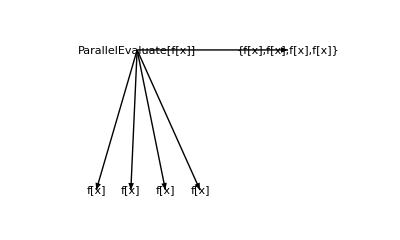

```mathematica
diagram["ParallelEvaluate[f[x]]",{"f[x]","f[x]","f[x]","f[x]"},"{f[x],f[x],f[x],f[x]}"]
```

### Code Examples

```mathematica
ParallelEvaluate[{$KernelID,RandomReal[]}]
```

```mathematica
ParallelEvaluate[h[n_]:={$KernelID,n^2}];
```

```mathematica
ParallelEvaluate[h[10]]
```

## How to Parallelise?

## Sequence Control: Fixed-Length Loops

Automatic distribution of iterations to workers.

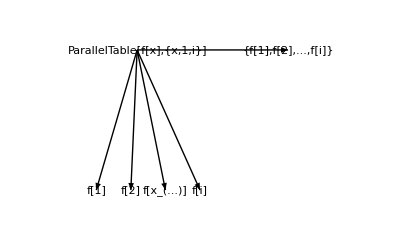

```mathematica
diagram["ParallelTable[f[x],{x,1,i}]",{"f[1]","f[2]","f[x_(...)]", "f[i]"},"{f[1],f[2],...,f[i]}"]
```

### Code Examples

#### ParallelTable

```mathematica
ParallelTable[i^2,{i,10}]
```

#### ParallelDo

```mathematica
ParallelDo[Print[i],{i,4}]
```

#### ParallelSum

```mathematica
ParallelSum[i^2,{i,1000}]
```

#### ParallelProduct

```mathematica
ParallelProduct[i,{i,100}]
```

#### ParallelMap

```mathematica
ParallelMap[f,Range[50,60]]
```

#### ParallelArray

```mathematica
ParallelArray[f,{3,2}]
```

## How to Parallelise?

## Sequence Control: Fixed-Length Loops

#### ParallelMap

```mathematica
ParallelMap[f,Range[50,60]]
```

#### ParallelArray

```mathematica
ParallelArray[f,{3,2}]
```

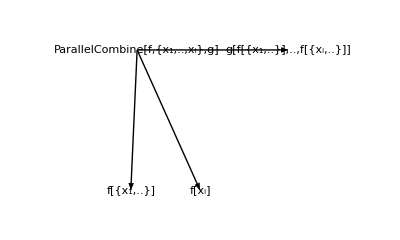

```mathematica
diagram["ParallelCombine[f,{x_1,..,x_i},g]",{"f[{x_1,..}]", "f[x_i]"},"g[f[{x_1,..}],..,f[{x_i,..}]]"]
```

#### ParallelCombine

```mathematica
ParallelCombine[f[##]&,{1,2,3,4,5,6,7,8,9,10},g]
```

## How to Parallelise?

## Manual Control

The user submits tasks and can set up wait conditions.

#### ParallelTry

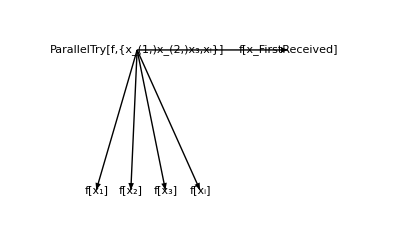

```mathematica
diagram["ParallelTry[f,{x_(1,)x_(2,)x_3,x_i}]",{"f[x_1]","f[x_2]","f[x_3]", "f[x_i]"},"f[x_FirstReceived]"]
```

```mathematica
ParallelTry[{Pause[5];NextPrime[#],$KernelID}&,{9899999999,9899999999,9899999999},3]
```

{{9900000001,4},{9900000001,3},{9900000001,2}}

#### ParallelSubmit, WaitAll, WaitNext

```mathematica
eids=Table[ParallelSubmit[{i},Length[FactorInteger[2^i-1]]],{i,181,184}]
```

-Graphics-

```mathematica
{res,id,eids}=WaitNext[eids]
```

-Graphics-

```mathematica
WaitAll[eids]
```

{11,5,11}

## Additional Functionality

### Global Variables

#### $KernelCount

Stores the number of subkernels that are available for parallel computations.

```mathematica
$KernelCount
```

#### $ProcessorCount

Gives the number of processor cores available on the system that can run a Wolfram kernel.

```mathematica
$ProcessorCount
```

### Manual Processes

#### LaunchKernels

Launches all configured parallel subkernels.

```mathematica
LaunchKernels[]
```

#### AbortKernels

Aborts all tasks active on parallel subkernels.

```mathematica
AbortKernels[]
```

#### Kernels

Gives a list of all active parallel subkernels.

```mathematica
Kernels[]
```

#### CloseKernels

Aborts all tasks active on parallel subkernels.

```mathematica
CloseKernels[]
```

```mathematica
Kernels[]
```

#### ParallelNeeds

Runs the Needs function in all parallel subkernels.

```mathematica
ParallelNeeds["SomePackage`"]
```

## Sharing State

#### DistributeDefinitions

Distributes the definitions of the defined symbols to all parallel subkernels. This is done automatically by many functions and is recursive:

```mathematica
f[x_]:=x^2;
```

```mathematica
DistributeDefinitions[f]
```

{f}

```mathematica
ParallelEvaluate[f[$KernelID]]
```

{1,4,9,16}

#### SetSharedVariable

Declares symbols whose definitions should be synchronised amongst all parallel subkernels.

```mathematica
ParallelEvaluate[x]
```

```mathematica
SetSharedVariable[x]
```

```mathematica
x=12
```

```mathematica
ParallelEvaluate[x]
```

#### SetSharedFunction

Declares functions whose definitions should be synchronised amongst all parallel subkernels.

```mathematica
ParallelEvaluate[g[x]]
```

```mathematica
SetSharedFunction[g]
```

```mathematica
g[x_]:=Style[x,Red]
```

```mathematica
ParallelEvaluate[g[$KernelID]]
```

## New in 12.2: Batch Computation

```mathematica
ServiceConnect["AWS", "New"]
```

ServiceObject[…]

```mathematica
env = RemoteBatchSubmissionEnvironment["AWSBatch",<|"JobQueue"->"arn:aws:batch:us-east-2:337830956718:job-queue/WolframJobQueue-7e156ef3cfdca27","JobDefinition"->"arn:aws:batch:us-east-2:337830956718:job-definition/WolframJobDefinition-beeadc6fbadaf65:1","IOBucket"->"mywolframbatchstack-wolframjobdatabucket-yz8qoysjpko"|>]
```

RemoteBatchSubmissionEnvironment[…]

```mathematica
job = RemoteBatchSubmit[env,1988^1988]
```

RemoteBatchJobObject[…]

```mathematica
job["JobStatus"]
```

Starting

```mathematica
job["JobStatus"]
```

Succeeded

```mathematica
job["EvaluationResult"]
```

178551524186178856440874321390111562424011992746385766185488679670492248629302591868498272055046482474211106742094860217457928680807374232460172692019819925188778676673692157008725655670433023618053948632337740569072239952313658867274429903393652865065345194165014819518639460976631961614777493544693327308181584538078171728239014252777920833200270668099875483944701892291462416351820193250855375229424230698849967370791758125026072013362883433801070066132835778891208890042902238862050188798144930018220201547176272440366563144249523218354733543870282023044580031370049895982594181145709684980618514343503461345720006139467437172553557827663421651138165371172162065776325878402405935325770588124667046262770527807355794540661993433722678261274786497196564443550951969890187591692905667547449195111745005393473123645798632370332820589738823845115963881830365265746945567531617208482673650377529150779171200303978803096719105924042949228536872156538676521940889621990568476921051488026818119397938178191350846156625932830263388322292074037551640021194674756091573696979096068376784944237435464579310234214472725897346051786739194123557306944306387568673186397944502339932062548205617337862660550421277708154237783467410705604158576740911700824722151339888951115324105673868417294732510124103498921033991875286293645880609459498546974175187847583795589992695453747575322834029682848761154236606025374757681833942406486970397352628687603503147272558317629621852446634560122698219313602152577455118788628595930161408308561929283913775056794012885890679745490742886053366891714773182788523882427982811766752561222061396983165138224265984505130595968804922596274526732301395703037783240449283407499139354638683542195014927938127453514307082540379129854152549188659650134103617739664114740153341355147214676237387994184269332806968080627558811531331068145549390359551299143958691492299535589423322207879147222416790480567918267211260335107218091682458602140966040128569821476133187714284438221325514348472117534894778732994769642622755939933320632102487638382889224787323192653723881880597729250631817582064052862428138126201205499009243693455649056244828092399843476402503561175013012824580887862794287222718396040677113482877964833908346047766157769093890717804644161180857357120737861164543914636299750451235294641598398928250563561112915025908358704274309223731720186253024256834945752953191505830124654135228062306627480477893428383721037024325466688637322317262135952764359409640763178837620847571558693795170742034401253720982626927378896292166796844984912588077671865821891845878155361799409691331685544887701089674841121059337736193461053829373067288572803813830130063217173084048881200974305949098212463167604239205017186776983332962654564973694326570975481593583528898001459450076018721152439286635822710317007877238624377463404188914439501040719694504279104456533309842263398741239074376862989444429538362447742622113068922377033117759827832835512768716987483385572590546569962753219851476053091170512818655175715442724784471296455962852003081090922033882627524976918899958866701499100818801783378915436978742966073550493448344442585364103275922217167081087072257917476150555376305145923709642656459519865936462766671940390817426471922214164823966556678002001393099920450450386316050670353875704429883178059702727848032352307813490342075509425650381625273649069585958963278015308088729190574081938217364515649549917536935335797027289023322905943776622915515243010901583111755534143439143271482708225314067630916466227642020624955215998413251416227773256921291557061467520697671790869649764588273175437957626376629506745240837894750696578007416528937313463692212883665759265554764632456669960164511593724609060421703870374416705009070107989949949001847788141324355671005493476289853492067965845665383650827403568562873513074130673758757264010403594468076900728135288708490428550295941677529294901951926767555680391272889460183288447329572337882263969475144640357828242871054771132470168680322701090092905764651293812984970746662052251534269449535407876413365185635445022526354744416378876663504071421170349525542378386154891924481091185468805882567431737334981045160983783766019712371326385704009788393106163836576577340035350748506544698095795323860420945887281701440654744592480195828204243176439620354574436694242162258962301444543221720716327420859014216265517205931514001143681830088686599472178595286208607411152210440724680988342002829606950277336871575601425667007867773702067342430419906492856466450081125570288136857248745472524523581969833910846217726891067674892811804514349285185478069862158149037568907128644261093524654890204114361157952228459055348433366826059749931475010290027826909541975005960496470316612811253509188701684914700806841901974643179031769081015956677658176352266559983686366959325375958656817745898323480514898211600981035684869958862121675293106136513487971620566700925088693601453356497018148028618302165943702800191421081013038375394960704223959420069913416840300785932200373919879853011576431513667450681378869178095746648547852368316234456748909294994954192272259623026985924622492319176043957158203767474714818890774523185475068182310351442106575621187998539287645915896948629434051896126658117281722105065605774921353904002000392348595985705835409246599631896646071996606444053995017678982454766949354515142885906871660477496412863857822347012020026750117581977410123382625163408694932496690060465134981538671202460903807899262969184417410540304336677171456566430828274224070100439777435909960113685532765138737744937235157064735512567149167966889270545424500509311327293152240015797245142256235725133939520173882100768836347398085667524279031160065490473108803955887856110745650862449186439335614944143276544493175998316577179257481126289594881224442618470981273805314751174625982541134249731368522024517407058432561630179076966426605677028421294512691791641079381657201233667525380166030728686255199638782804868389204084202589979249865792950423840363663789869570120938370371233971857702454654704206690993643835437954550736965351546404478020238922154556817723529215426090501914176561157694244071389749796377764833155294475712225908536231651857816025038315673607808186795719127076327973225423254657259186446136493436084089940585948182360039412580507453330593235655327539522112265877515366168183881354852577846879517262604909046252475558819558719323024115790178470626249928230114706790521616931224385558598853360432063812786650262858470834593807454813120251528787832416757149495824329964810266925370444560933584896

## Parallel Kernel Configurator

To access the parallel kernel configuration interface, use the Evaluation drop-down menu and choose Parallel Kernel Configuration….

## Performance Considerations

There are a few main things to consider that will affect the performance of a parallel computation:

Large vs small questions

Large vs small answers

Long vs short communication

## Small Grain vs Large

### Small Grain

Small batch size = more efficient use of CPU.

Larger amount of communication needed:

```mathematica
Parallelize[Map[Labeled[Framed[#],$KernelID]&,Range[10]],Method->"FinestGrained"]
```

### Large Grain

Larger batch size = less efficient use of CPU.

Smaller amount of communication needed:

```mathematica
Parallelize[Map[Labeled[Framed[#],$KernelID]&,Range[10]],Method->"CoarsestGrained"]
```

### Custom Grain Size

Limiting size of batches:

```mathematica
Parallelize[Table[Labeled[Framed[i],$KernelID],{i,12}],Method->"EvaluationsPerKernel"->2]
```

Limiting the number of evaluations:

```mathematica
Parallelize[Table[Labeled[Framed[i],$KernelID],{i,18}],Method->"ItemsPerEvaluation"->5]
```

## Init

```mathematica
ts[expr_,pos_]:=Text[Framed[Style[expr,FontFamily->"Courier",FontSize->Scaled[0.025]],Background->LightYellow,RoundingRadius->5],pos];
```

```mathematica
diagram[head_String,leaf_List,out_String]:=
Graphics[
	{
		Table[
			{
				Arrowheads[{0,-.03,.03,0}],
				Arrow[{{0,1},{5.5/Length@leaf*i-3,0}}],
				ts[leaf[[i]],{5.5/Length@leaf*i-3,0}]
			},
			{i,1,Length@leaf}
		],
		Arrowheads[List@{0.03,.6}],
		Arrow[{{0,1},{6,1}}],
		ts[head,{0,1}],
		ts[out,{6,1}]
	},
	PlotRange->{{-4,9},{-0.2,1.2}},
	AspectRatio->0.6,
	ImageSize->Scaled[0.9]
];
```